```mathematica
<<JLink`
```

```mathematica
LoadJavaClass["java.awt.geom.Ellipse2D"];
```

```mathematica
LoadJavaClass["java.awt.geom.PathIterator"];
```

```mathematica
renderJavaShape[shape_,flatness_:Automatic]:=(
lastPoint=Null;
paths={};
coordsObj=JavaNew["[D",6];
If[flatness===Automatic,
pi=shape@getPathIterator[Null];
,
pi=shape@getPathIterator[Null,flatness];
];
While[!pi@isDone[],
res=pi@currentSegment[coordsObj];
coords=JavaObjectToExpression[coordsObj];
Switch[res,
PathIterator`SEGUMOVETO,
path={};
lastPoint=coords[[1;;2]];
,
PathIterator`SEGUCLOSE,
paths=paths~Append~path;
path=Null;
,
PathIterator`SEGULINETO,
path=path~Append~Line[{lastPoint,coords[[1;;2]]}];
lastPoint=coords[[1;;2]]
,
PathIterator`SEGUQUADTO,Print[quadto];,
PathIterator`SEGUCUBICTO,
path=path~Append~BezierCurve[{lastPoint}~Join~Partition[coords,2]];
lastPoint=coords[[5;;6]]
];
pi@next[]
];
paths
)
```

## demonstrates problem

```mathematica
a=JavaNew["java.awt.geom.Area"];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",100.0,100.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",190.0,100.0,100.0,100.0]]];
a@add[JavaNew["java.awt.geom.Area",JavaNew["java.awt.geom.Ellipse2D$Double",220.0,180.0,100.0,100.0]]];
```

```mathematica
g=renderJavaShape[a]
```

{{BezierCurve[{{195.,128.179},{195.,128.179},{195.,128.179},{195.,128.179}}],Line[{{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,128.179},{195.,128.179},{195.,128.179},{195.,128.179}}]},{BezierCurve[{{150.,100.},{122.386,100.},{100.,122.386},{100.,150.}}],BezierCurve[{{100.,150.},{100.,177.614},{122.386,200.},{150.,200.}}],BezierCurve[{{150.,200.},{169.791,200.},{186.896,188.501},{195.,171.821}}],Line[{{195.,171.821},{195.,171.821}}],BezierCurve[{{195.,171.821},{201.797,185.812},{214.928,196.158},{230.665,199.13}}],Line[{{230.665,199.13},{230.665,199.13}}],BezierCurve[{{230.665,199.13},{223.984,207.631},{220.,218.35},{220.,230.}}],BezierCurve[{{220.,230.},{220.,257.614},{242.386,280.},{270.,280.}}],BezierCurve[{{270.,280.},{297.614,280.},{320.,257.614},{320.,230.}}],BezierCurve[{{320.,230.},{320.,205.576},{302.488,185.242},{279.335,180.87}}],Line[{{279.335,180.87},{279.335,180.87}}],BezierCurve[{{279.335,180.87},{286.016,172.369},{290.,161.65},{290.,150.}}],BezierCurve[{{290.,150.},{290.,122.386},{267.614,100.},{240.,100.}}],BezierCurve[{{240.,100.},{220.209,100.},{203.104,111.499},{195.,128.179}}],Line[{{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,128.179},{186.896,111.499},{169.791,100.},{150.,100.}}]}}

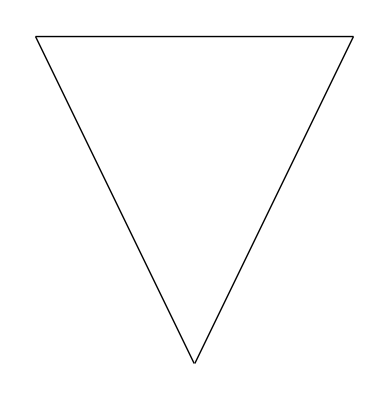

```mathematica
Graphics[g[[1]]]
```

## using AreaX

```mathematica
AddToClassPath["C:\\Users\\brenton\\DeadlockWorkspace\\AreaX\\bin\\"];
```

```mathematica
a=JavaNew["com.bric.geom.AreaX"];
a@add[JavaNew["com.bric.geom.AreaX",JavaNew["java.awt.geom.Ellipse2D$Double",100.0,100.0,100.0,100.0]]];
a@add[JavaNew["com.bric.geom.AreaX",JavaNew["java.awt.geom.Ellipse2D$Double",190.0,100.0,100.0,100.0]]];
a@add[JavaNew["com.bric.geom.AreaX",JavaNew["java.awt.geom.Ellipse2D$Double",220.0,180.0,100.0,100.0]]];
```

```mathematica
g=renderJavaShape[a]
```

{{BezierCurve[{{150.,100.},{122.386,100.},{100.,122.386},{100.,150.}}],BezierCurve[{{100.,150.},{100.,177.614},{122.386,200.},{150.,200.}}],BezierCurve[{{150.,200.},{169.791,200.},{186.896,188.501},{195.,171.821}}],Line[{{195.,171.821},{195.,171.821}}],BezierCurve[{{195.,171.821},{201.797,185.812},{214.928,196.158},{230.665,199.13}}],Line[{{230.665,199.13},{230.665,199.13}}],BezierCurve[{{230.665,199.13},{223.984,207.631},{220.,218.35},{220.,230.}}],BezierCurve[{{220.,230.},{220.,257.614},{242.386,280.},{270.,280.}}],BezierCurve[{{270.,280.},{297.614,280.},{320.,257.614},{320.,230.}}],BezierCurve[{{320.,230.},{320.,205.576},{302.488,185.242},{279.335,180.87}}],Line[{{279.335,180.87},{279.335,180.87}}],BezierCurve[{{279.335,180.87},{286.016,172.369},{290.,161.65},{290.,150.}}],BezierCurve[{{290.,150.},{290.,122.386},{267.614,100.},{240.,100.}}],BezierCurve[{{240.,100.},{220.209,100.},{203.104,111.499},{195.,128.179}}],Line[{{195.,128.179},{195.,128.179}}],BezierCurve[{{195.,128.179},{186.896,111.499},{169.791,100.},{150.,100.}}]}}

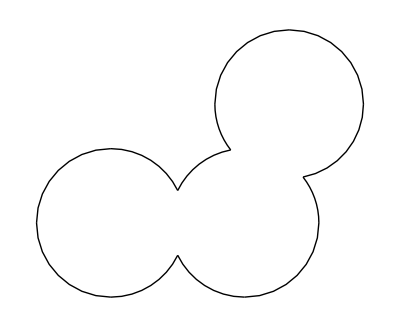

```mathematica
Graphics[g]
```

## more

```mathematica
custom=JavaNew["java.awt.geom.GeneralPath"]
```

«JavaObject[java.awt.geom.GeneralPath]»

```mathematica
custom@moveTo[200,150]
```

```mathematica
custom@curveTo[200.,177.61423749153965,177.61423749153965,200.,150.,200.]
custom@curveTo[122.38576250846033,200.,100.,177.61423749153965,100.,150.]
custom@curveTo[100.,122.38576250846033,122.38576250846033,100.,150.,100.]
custom@curveTo[177.61423749153965,100.,200.,122.38576250846033,200.,150.]
```

```mathematica
custom@closePath[]
```

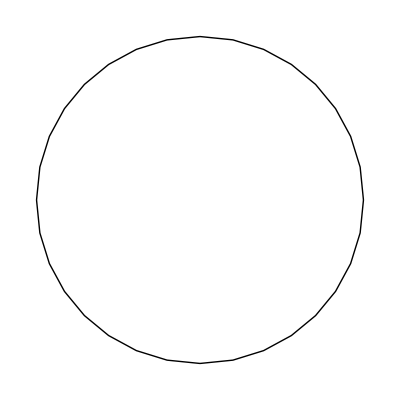

```mathematica
Graphics[renderJavaShape[custom]]
```

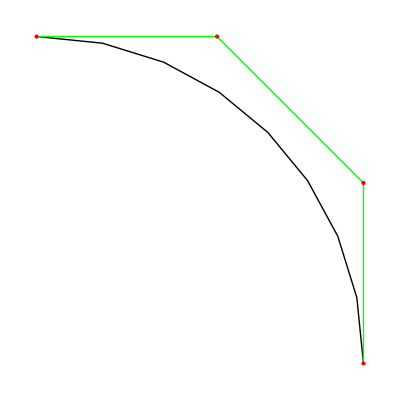

```mathematica
pts={{200,150},{200.,177.61423749153965},{177.61423749153965,200.},{150.,200.}};
Graphics[{BezierCurve[pts],Green,Line[pts],Red,Point[pts]}]
```